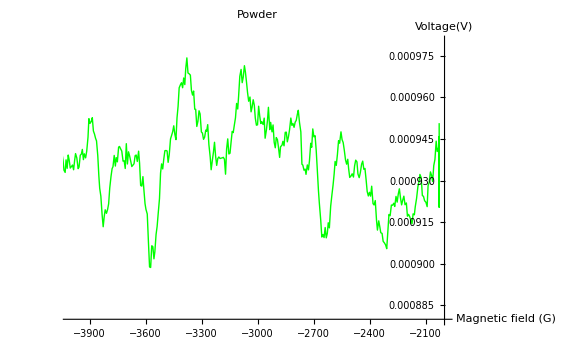

```mathematica
ten=Import["C:\\Users\\Peggy\\Desktop\\M2.6 ectron Spin Resonance\\EPRdata\\poeder\\10", "Table"];
b10=Take[ten, {5,397}];
pb1=ListLinePlot[b10,PlotRange->{{-4000,-2000}, {0.00088,0.00098}} ,LabelStyle->{10,GrayLevel[0],Bold},ImageSize->Large, AspectRatio->1/GoldenRatio, PlotLabel->"Powder" ,   AxesLabel->{"Magnetic field (G)", " Voltage(V)"}, PlotStyle->Directive[Thin,PointSize[Small],Green]]
```

```mathematica
peaks=FindPeaks[Table[datapoint[[2]],{datapoint,b10}]]
```

{{1,0.000932569},{6,0.000939282},{12,0.000939174},{19,0.000939697},{25,0.000941204},{34,0.000952629},{59,0.000942271},{65,0.000943269},{67,0.00094034},{74,0.000939183},{88,0.000906488},{101,0.000940812},{108,0.000949712},{120,0.000974185},{131,0.00095513},{139,0.000950133},{145,0.000943777},{153,0.000938353},{157,0.000945002},{169,0.000970031},{172,0.000971374},{180,0.0009591},{185,0.00095677},{194,0.000956376},{201,0.000945477},{210,0.000947417},{214,0.000952509},{221,0.000955299},{234,0.000948592},{245,0.000913057},{259,0.000947536},{272,0.000937335},{278,0.000936992},{310,0.000927015},{314,0.000924362},{328,0.000932193},{342,0.000944198},{348,0.000925238},{351,0.000924634},{356,0.000932504},{359,0.000925839},{371,0.000940014},{378,0.000943695},{381,0.000945779},{393,0.000950668}}

```mathematica
peakindices=Table[peak[[1]],{peak,peaks}]
```

{1,6,12,19,25,34,59,65,67,74,88,101,108,120,131,139,145,153,157,169,172,180,185,194,201,210,214,221,234,245,259,272,278,310,314,328,342,348,351,356,359,371,378,381,393}

```mathematica
peakpoints=Table[b10[[i]],{i,peakindices}]
```

{{-4067.56,0.000932569},{-4046.3,0.000939282},{-4014.03,0.000939174},{-3974.78,0.000939697},{-3938.46,0.000941204},{-3885.1,0.000952629},{-3739.55,0.000942271},{-3703.09,0.000943269},{-3691.35,0.00094034},{-3650.19,0.000939183},{-3566.97,0.000906488},{-3490.9,0.000940812},{-3449.17,0.000949712},{-3379.,0.000974185},{-3313.88,0.00095513},{-3267.45,0.000950133},{-3231.02,0.000943777},{-3183.8,0.000938353},{-3160.24,0.000945002},{-3088.77,0.000970031},{-3071.,0.000971374},{-3023.99,0.0009591},{-2994.92,0.00095677},{-2942.51,0.000956376},{-2900.39,0.000945477},{-2846.78,0.000947417},{-2822.53,0.000952509},{-2782.69,0.000955299},{-2705.08,0.000948592},{-2638.8,0.000913057},{-2554.22,0.000947536},{-2475.33,0.000937335},{-2437.88,0.000936992},{-2241.73,0.000927015},{-2217.61,0.000924362},{-2131.74,0.000932193},{-2044.71,0.000944198},{-2028.96,0.000925238},{-2028.85,0.000924634},{-2028.74,0.000932504},{-2028.71,0.000925839},{-2028.68,0.000940014},{-2028.67,0.000943695},{-2028.67,0.000945779},{-2028.67,0.000950668}}

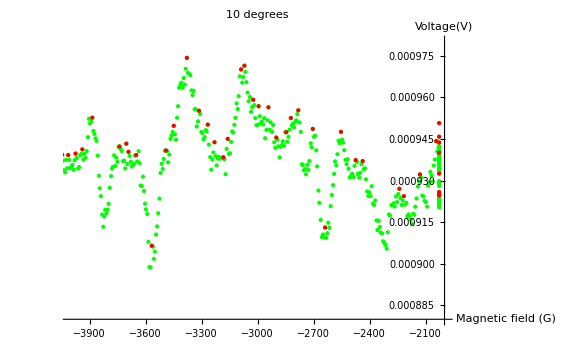

```mathematica
Show[pb1,ListPlot[peakpoints,PlotStyle->Directive[Thin,PointSize[Medium],Red]]]
```

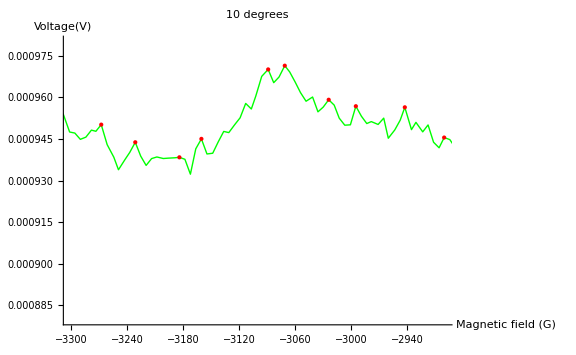

```mathematica
Show[pb1,ListPlot[peakpoints,PlotStyle->Directive[Thin,PointSize[Medium],Red]],PlotRange->{{-3300,-2900}, {0.00088,0.00098}} ,ImageSize->Large, AspectRatio->1/GoldenRatio]
```